```mathematica
dataUpTo7=Import[FileNameJoin[{NotebookDirectory[],"data",ToString[#]<>"-points.csv"}]]&/@Range[1,7]
```

```mathematica
plotFacetVert[data_,dim_]:=Show[Plot[(2^(dim+1)×dim)/x,{x,1,2^(dim+1)},PlotRange->All,PlotStyle->{LightBlue,Dashed}],ListPlot[data,PlotStyle->{PointSize[0.01],Yellow},AxesOrigin->{0,0}],PlotRange->{{0,2^dim+2},{0,2^dim+2}},AspectRatio->1,AxesOrigin->{0,0},AxesStyle->{{Bold,White},{Bold,White}},AxesLabel->(Style[#,White,Background->Black]&/@{"Facets","Vertices"}),GridLines->Automatic,GridLinesStyle->Gray,Background->Black,PlotLabel->Style["Facets and vertices of 2-level polytopes in dim "<>ToString[dim],White,Background->Black],ImageSize->600]
```

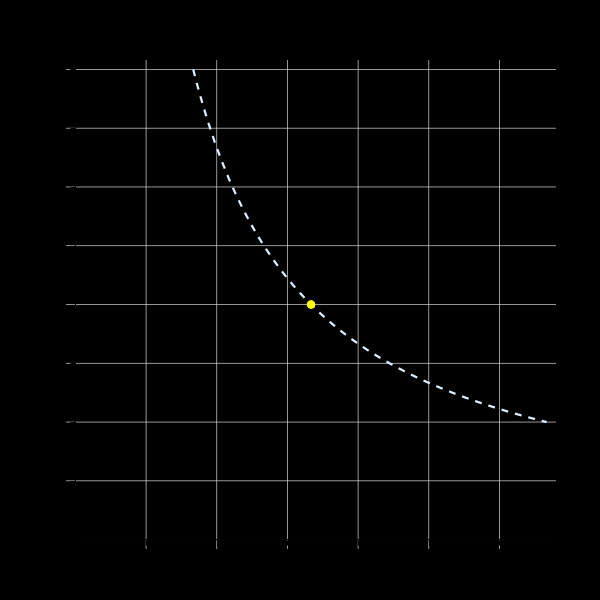
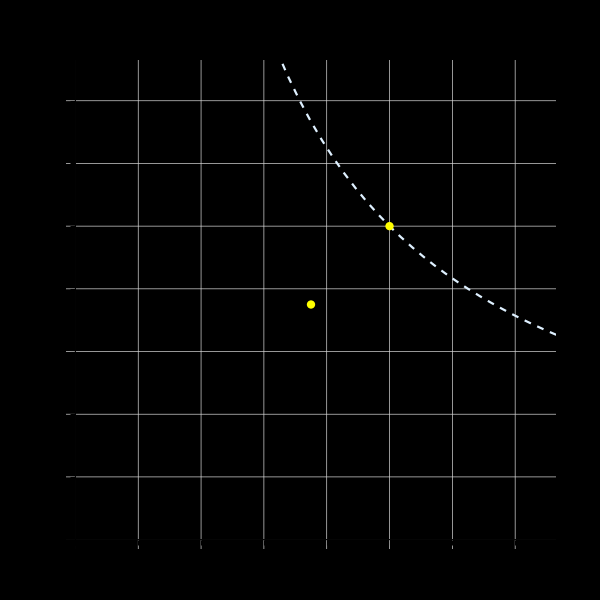
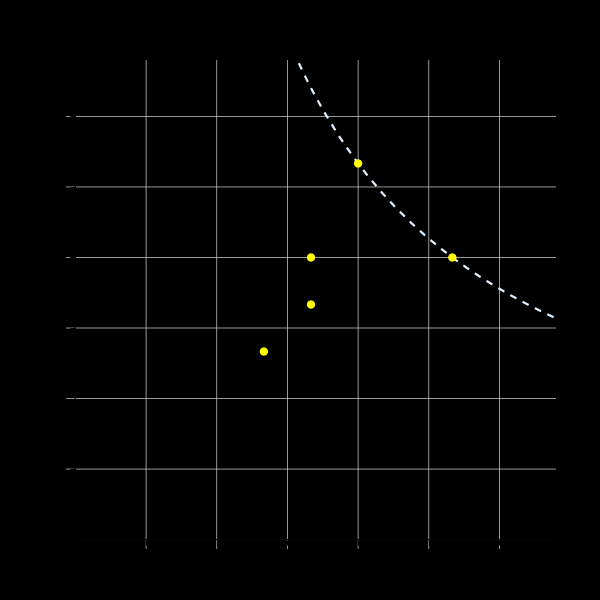
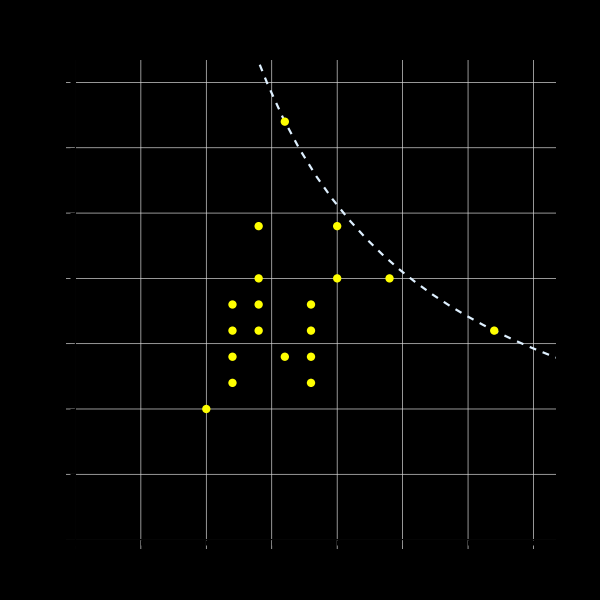
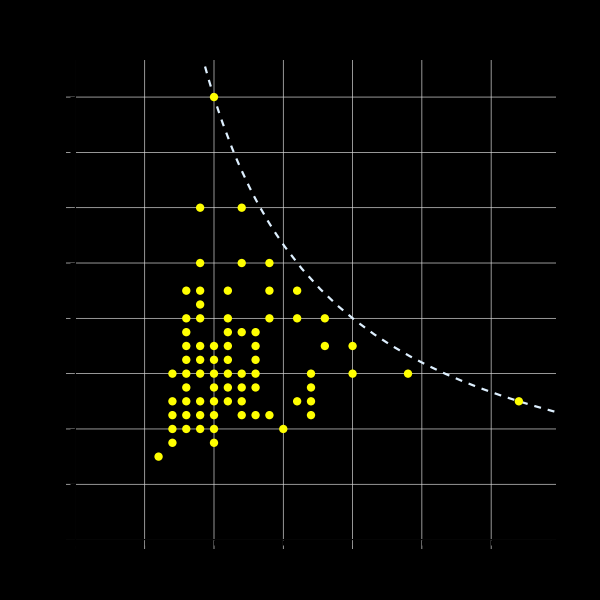
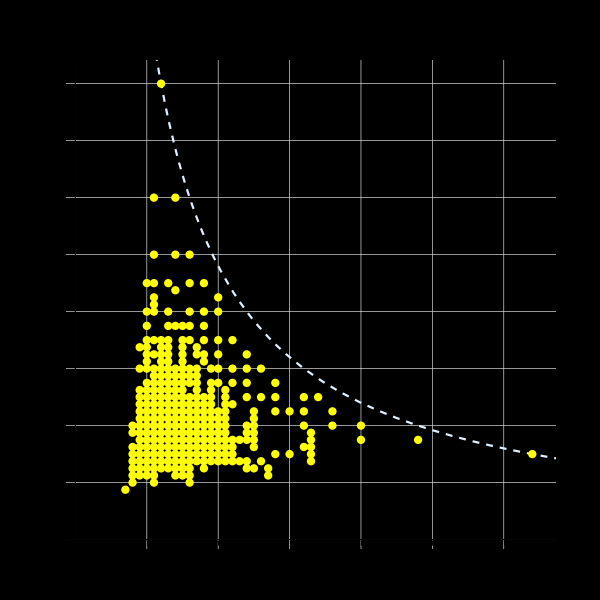
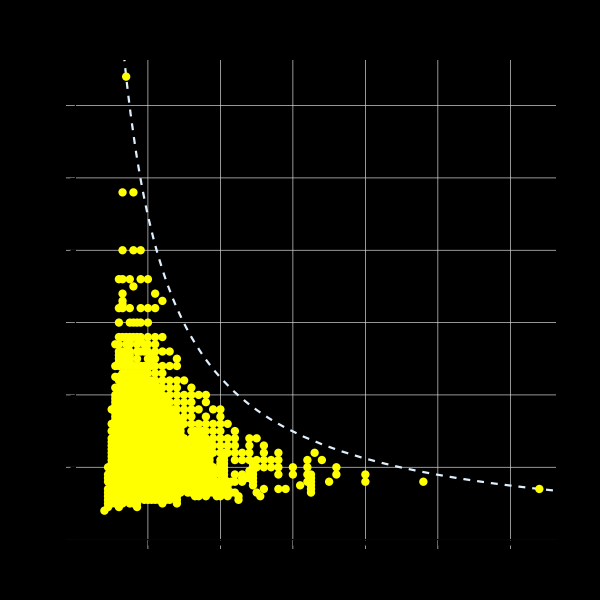
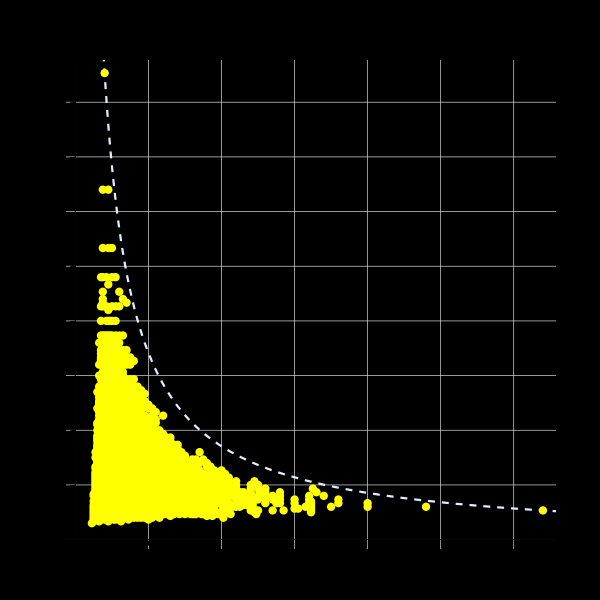

```mathematica
MapIndexed[plotFacetVert[#1,#2[[1]]]&,facetVertData]
```

```mathematica
MapIndexed[Export[FileNameJoin[{NotebookDirectory[],"2level-vert-facet-plots-"<>ToString[#2[[1]]]<>".jpg"}],#1]&,%];
```

```mathematica
points8=Import[FileNameJoin[{NotebookDirectory[],"data","8-points.csv"}]];
```

```mathematica
facetVertData=DeleteDuplicates/@Join[dataUpTo7,{points8}];
```

```mathematica
DumpSave[FileNameJoin[{NotebookDirectory[],"data","facet-vert-data-1to8.mx"}],facetVertData];
```

```mathematica
minProdData=DeleteDuplicates/@Map[{Min[#],#[[1]]#[[2]]}&,facetVertData,{2}];
maxProdData=DeleteDuplicates/@Map[{Max[#],#[[1]]#[[2]]}&,facetVertData,{2}];
```

```mathematica
vertProdData=DeleteDuplicates/@Map[{#[[2]],#[[1]]#[[2]]}&,facetVertData,{2}];
splitmaxProdData=DeleteDuplicates/@Map[{If[#[[1]]>#[[2]],#[[1]],-#[[2]]],#[[1]]#[[2]]}&,facetVertData,{2}];
```

```mathematica
fvdifProdData=Map[{#[[1]]-#[[2]],#[[1]]#[[2]]}&,facetVertData,{2}];
```

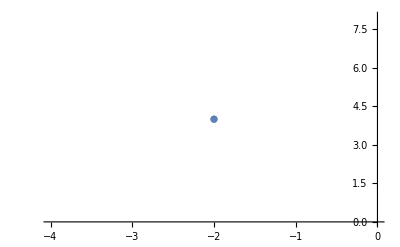
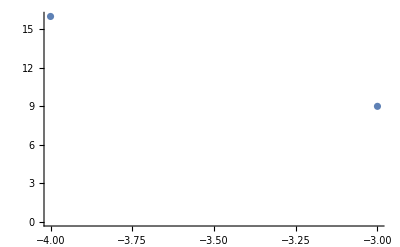
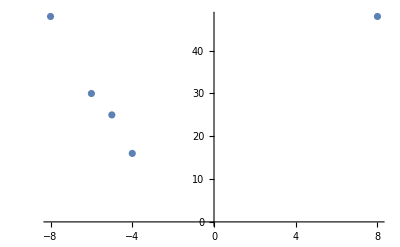
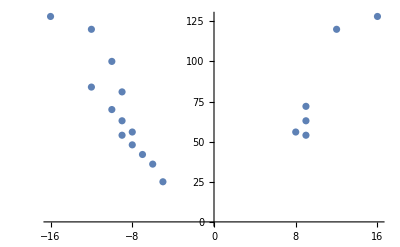
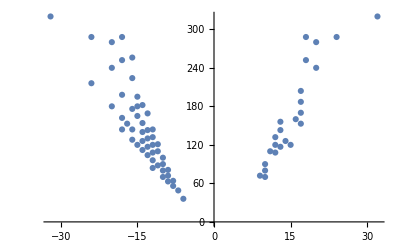
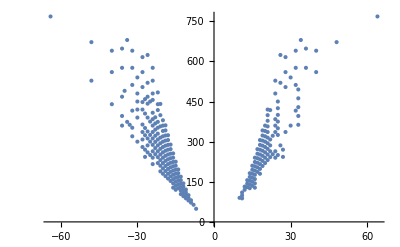
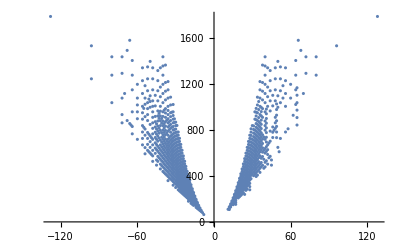
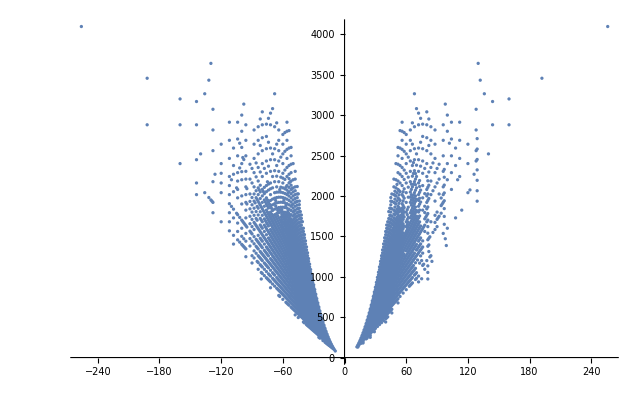

```mathematica
ListPlot[#,PlotRange->All,AxesOrigin->{0,0}]&/@splitmaxProdData
```

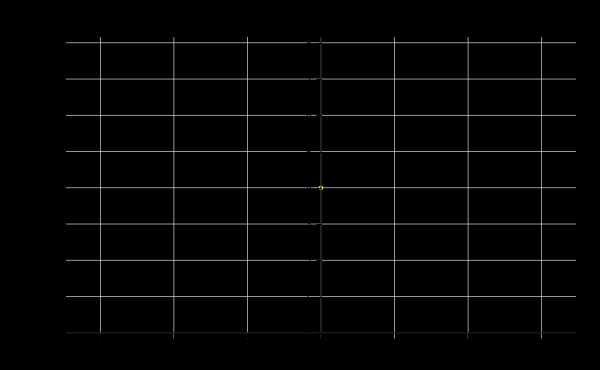
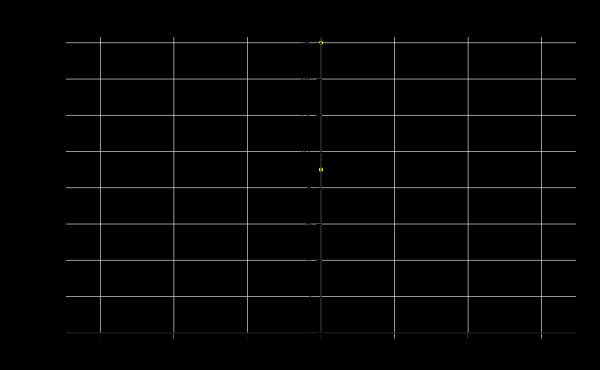
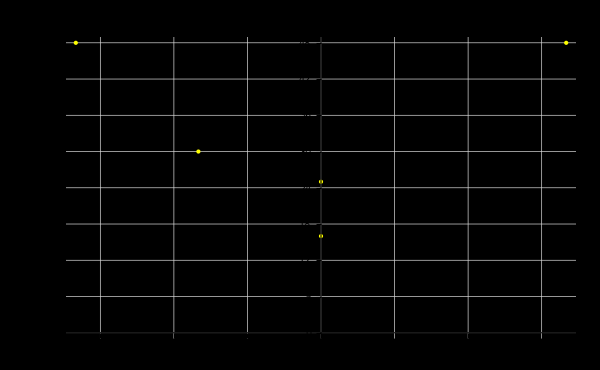
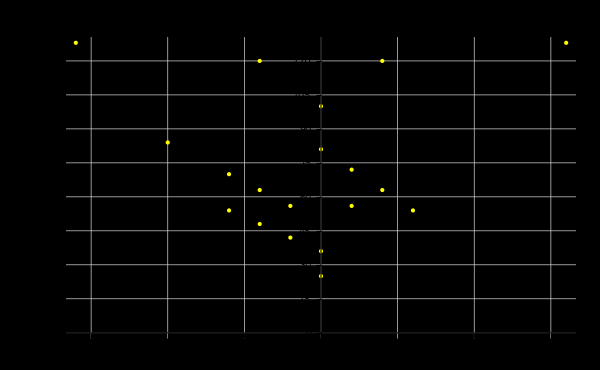
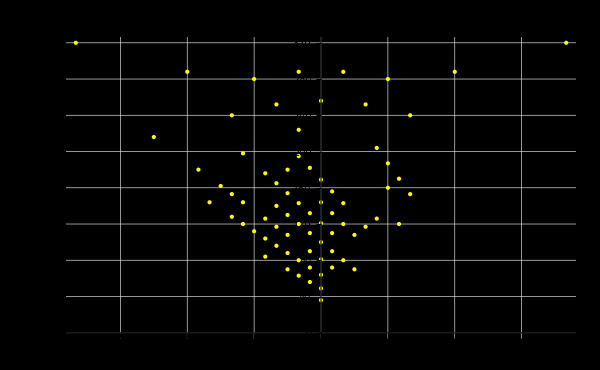
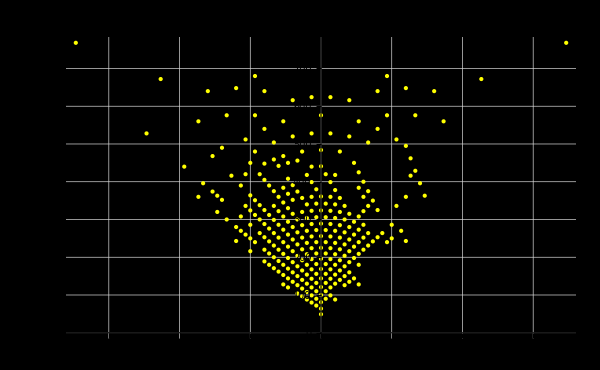
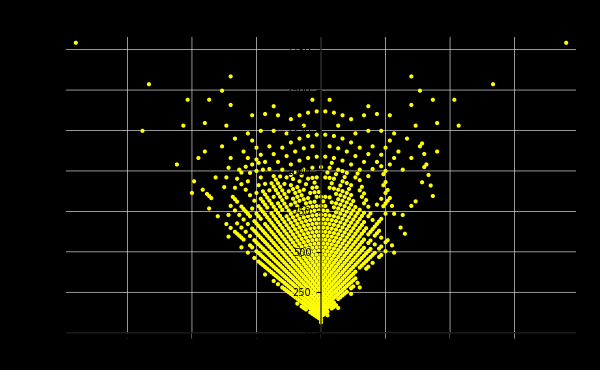
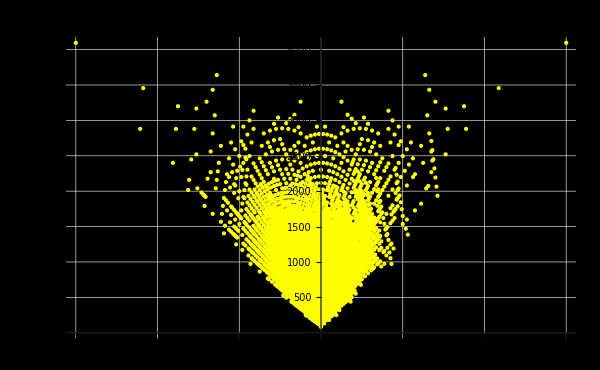
{-Graphics-f-v,-Graphics-f-v,-Graphics-f-v,-Graphics-f-v,-Graphics-f-v,-Graphics-f-v,-Graphics-f-v,-Graphics-f-v}

```mathematica
MapIndexed[Labeled[ListPlot[(pt|->Tooltip[{pt[[1]]-pt[[2]],Times@@pt},pt])/@#1,PlotRange->All,PlotStyle->{Yellow,PointSize[0.005]},Background->Black,AxesStyle->White,GridLines->Automatic,GridLinesStyle->Gray,AxesOrigin->{0,0},ImageSize->600,PlotLabel->Style["Difference vs Product in dim "<>ToString[#2[[1]]],White,Background->Black],AxesLabel->{None,"f·v"}],Style["f-v",White,Background->Black],Background->Black]&,facetVertData]
```

```mathematica
MapIndexed[Export[FileNameJoin[{NotebookDirectory[],"2level-dif-prod-plot-"<>ToString[#2[[1]]]<>".jpg"}],#1,Background->Black]&,%];
```

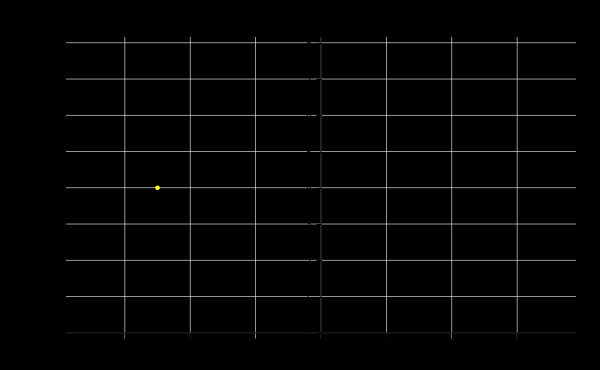
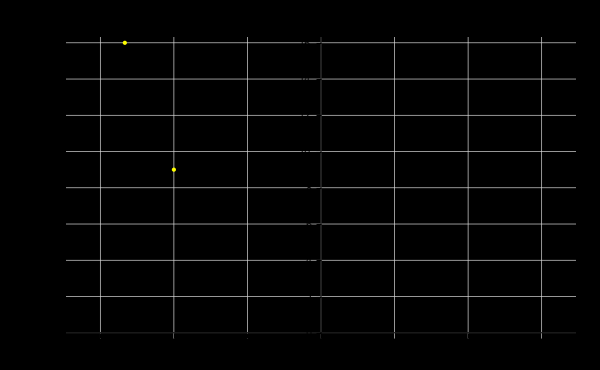
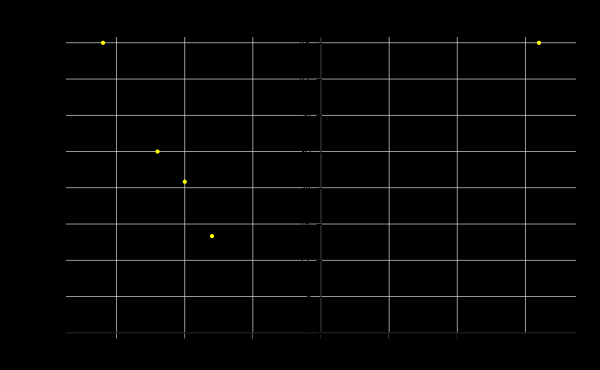
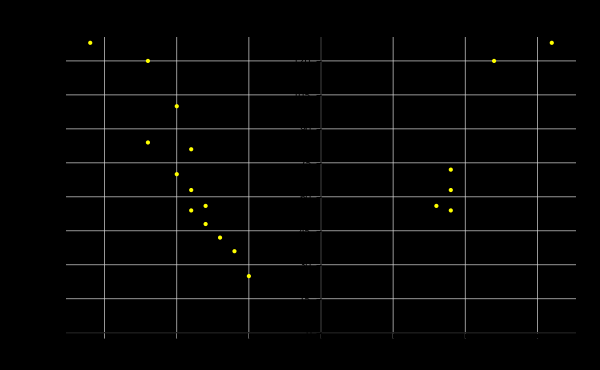
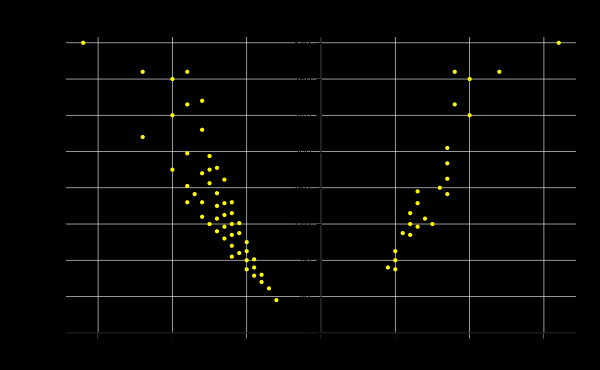
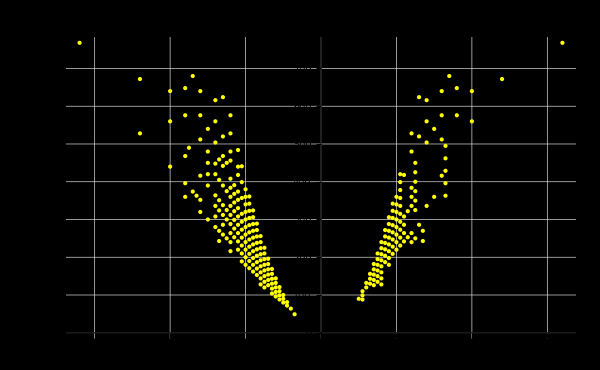
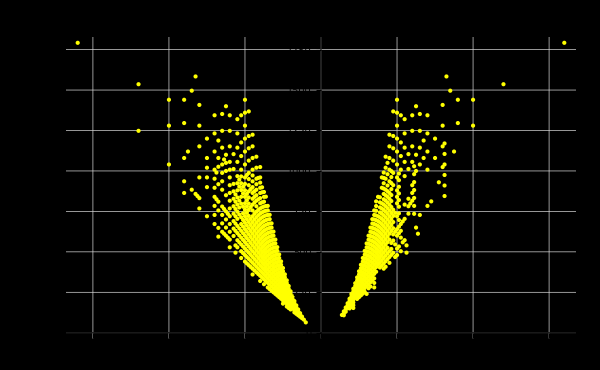
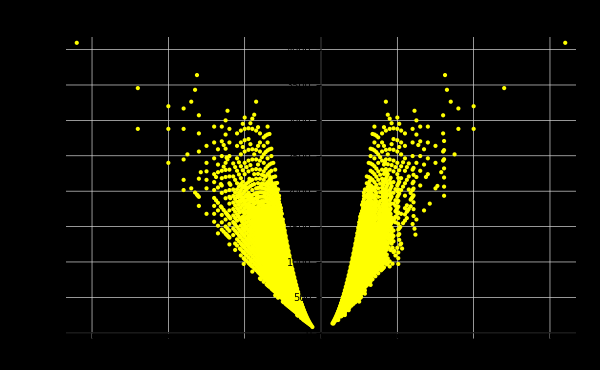
{-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v),-Graphics-(-1)^(f > v)max(f,v)}

```mathematica
MapIndexed[Labeled[ListPlot[(pt|->Tooltip[{If[pt[[1]]>pt[[2]],pt[[1]],-pt[[2]]],Times@@pt},pt])/@#1,PlotRange->{{-2^(#2[[1]])-1,2^(#2[[1]])+1},All},PlotStyle->{Yellow,PointSize[0.005]},Background->Black,AxesStyle->White,GridLines->Automatic,GridLinesStyle->Gray,AxesOrigin->{0,0},ImageSize->600,PlotLabel->Style["Max vs Product in dim "<>ToString[#2[[1]]],White,Background->Black],AxesLabel->{None,"f·v"}],Style["(-1)^(f > v)max(f,v)",White,Background->Black],Background->Black]&,facetVertData]
```

```mathematica
MapIndexed[Export[FileNameJoin[{NotebookDirectory[],"2level-max-prod-plot-"<>ToString[#2[[1]]]<>".jpg"}],#1,Background->Black]&,%];
```

```mathematica
peculiarSzs=<|4->{{8,16},{10,12}(*?*)},5->{{10,32},{16,18}},6->{{12,64},{20,34},{24,26}(*?*)},7->{{14,128},{24,66},{36,40}},8->{{16,256},{28,130},{48,68}}|>;
```

```mathematica
{2(#-0),2^#}&/@{4,5,6,7,8}
```

{{8,16},{10,32},{12,64},{14,128},{16,256}}

```mathematica
{4(#-1),2^(#-1)+2}&/@{5,6,7,8}
```

{{16,18},{20,34},{24,66},{28,130}}

```mathematica
{24,26}(*?*),{36,40},{48,68}
```

```mathematica
{12(#-4),2^(#-2)+4}&/@{6,7,8}
```

{{24,20},{36,36},{48,68}}

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
rawData1to7=Import[FileNameJoin[{"data",ToString[#]}]]&/@Range[7];
```

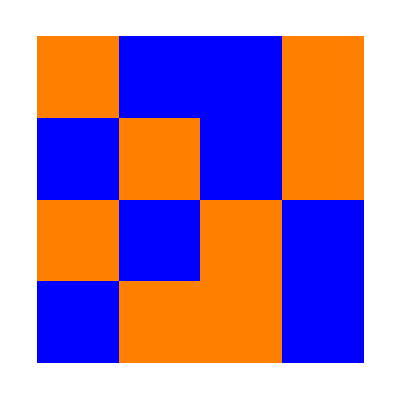
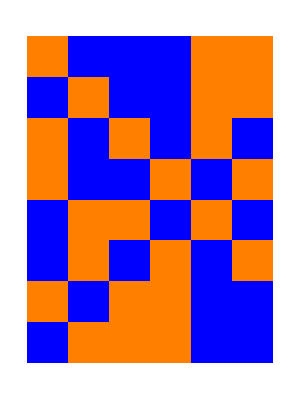
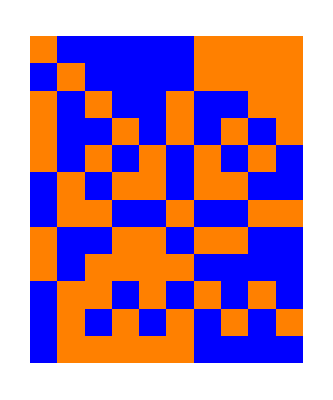
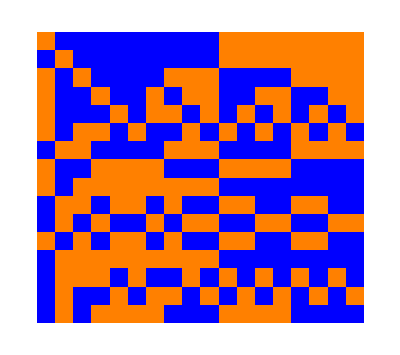
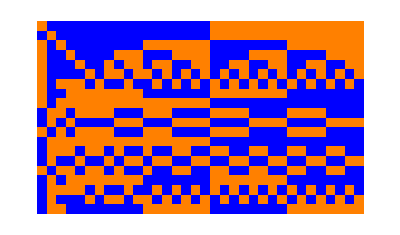
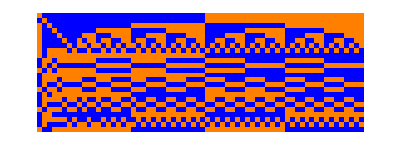

```mathematica
pecSecond=Table[ArrayPlot[Partition[IntegerDigits[Select[rawData1to7[[d]],#[[3;;4]]=={4(d-1),2^(d-1)+2}&][[1,-1]]],2^(d-1)+2],ColorRules->{1->Orange,0->Blue},Frame->False],{d,2,7}]
```

```mathematica
{4(#-1),2^(#-1)+2}&/@Range[8]
```

{{0,3},{4,4},{8,6},{12,10},{16,18},{20,34},{24,66},{28,130}}

Transformation of (presumably centrally symmetric) polytopes to 0-1 vectors

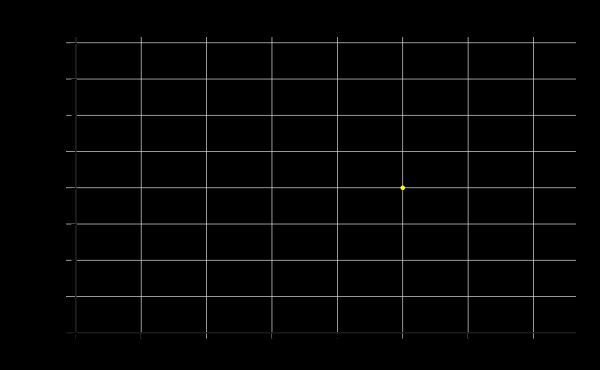
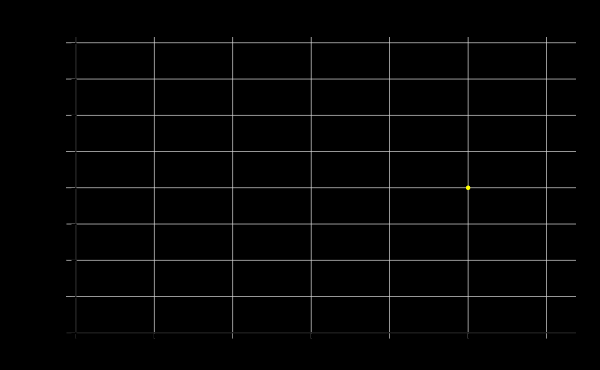
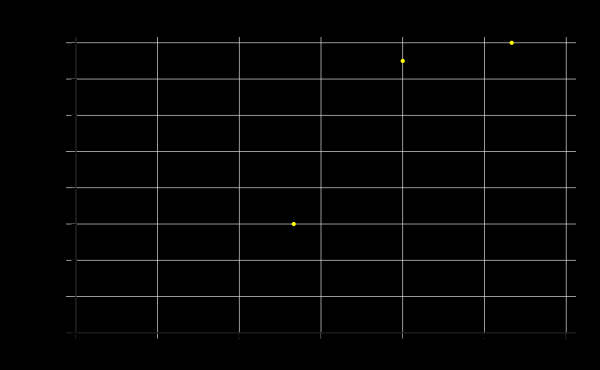
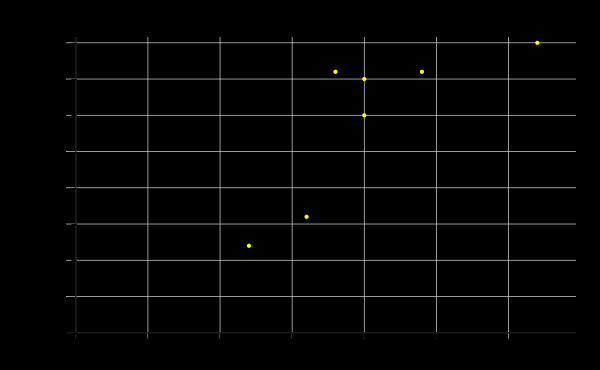
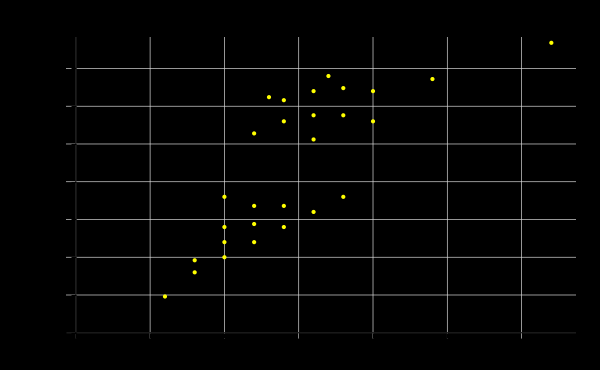
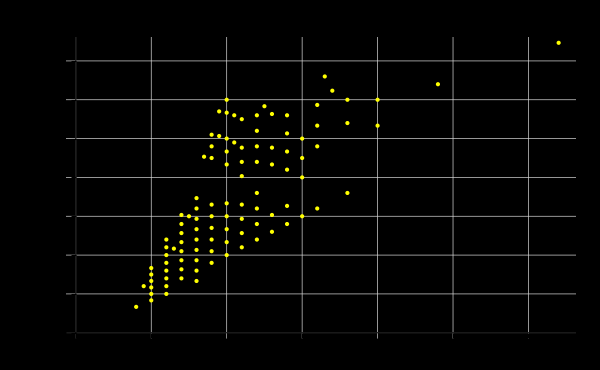
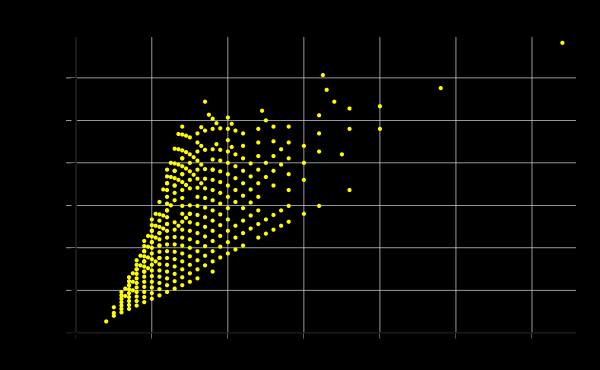
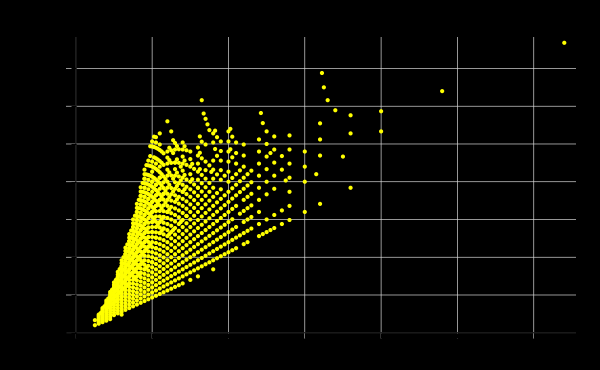
{-Graphics-max(a_1,a_2),-Graphics-max(a_1,a_2),-Graphics-max(a_1,a_2),-Graphics-max(a_1,a_2),-Graphics-max(a_1,a_2),-Graphics-max(a_1,a_2),-Graphics-max(a_1,a_2),-Graphics-max(a_1,a_2)}

```mathematica
MapIndexed[Labeled[ListPlot[(pt|->Tooltip[{Max@pt,Times@@pt},pt])/@#1,PlotRange->{{0,2^(#2[[1]])+1},All},PlotStyle->{Yellow,PointSize[0.005]},Background->Black,AxesStyle->White,GridLines->Automatic,GridLinesStyle->Gray,AxesOrigin->{0,0},ImageSize->600,PlotLabel->Style["Max vs Product for families arising from even polytopes in dim "<>ToString[#2[[1]]],White,Background->Black],AxesLabel->{None,"a_1·a_2"}],Style["max(a_1,a_2)",White,Background->Black],Background->Black]&,Map[If[And@@EvenQ[#],{(#[[1]])/2+1,#[[2]]},Nothing]&,facetVertData,{2}]]
```

```mathematica
MapIndexed[Export["families-from-even-max-vs-prod-"<>ToString[#2[[1]]]<>".jpg",#1,Background->Black]&,%];
```

```mathematica
Grid[Table[Style[{2^(d-k)+k,2^k(d-k+1)},White,Background->If[2^(d-k)+k>2^k(d-k+1),Red,Blue]],{d,0,11},{k,0,d}],Frame->All,Background->Black,FrameStyle->Gray]
```

{1,1} |  |  |  |  |  |  |  |  |  |  | 
{2,2} | {2,2} |  |  |  |  |  |  |  |  |  | 
{4,3} | {3,4} | {3,4} |  |  |  |  |  |  |  |  | 
{8,4} | {5,6} | {4,8} | {4,8} |  |  |  |  |  |  |  | 
{16,5} | {9,8} | {6,12} | {5,16} | {5,16} |  |  |  |  |  |  | 
{32,6} | {17,10} | {10,16} | {7,24} | {6,32} | {6,32} |  |  |  |  |  | 
{64,7} | {33,12} | {18,20} | {11,32} | {8,48} | {7,64} | {7,64} |  |  |  |  | 
{128,8} | {65,14} | {34,24} | {19,40} | {12,64} | {9,96} | {8,128} | {8,128} |  |  |  | 
{256,9} | {129,16} | {66,28} | {35,48} | {20,80} | {13,128} | {10,192} | {9,256} | {9,256} |  |  | 
{512,10} | {257,18} | {130,32} | {67,56} | {36,96} | {21,160} | {14,256} | {11,384} | {10,512} | {10,512} |  | 
{1024,11} | {513,20} | {258,36} | {131,64} | {68,112} | {37,192} | {22,320} | {15,512} | {12,768} | {11,1024} | {11,1024} | 
{2048,12} | {1025,22} | {514,40} | {259,72} | {132,128} | {69,224} | {38,384} | {23,640} | {16,1024} | {13,1536} | {12,2048} | {12,2048}

```mathematica
With[{hypBound=(2^(#1-#2)+#2)2^#2(#1-#2+1)&},hypBound[d,k]-2hypBound[d-1,k]//FullSimplify]
```

2^d+2^k k (1-d+k)

```mathematica
<<"data/facet-vert-data-1to8.mx"
```

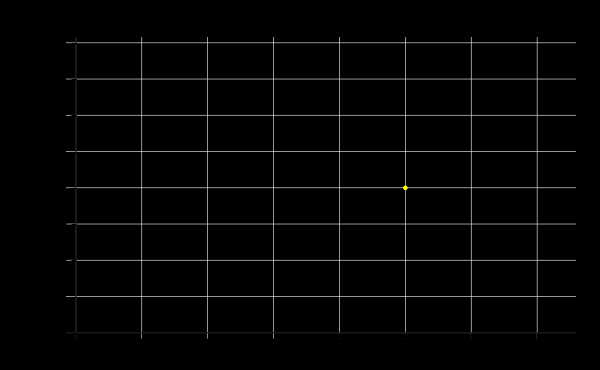
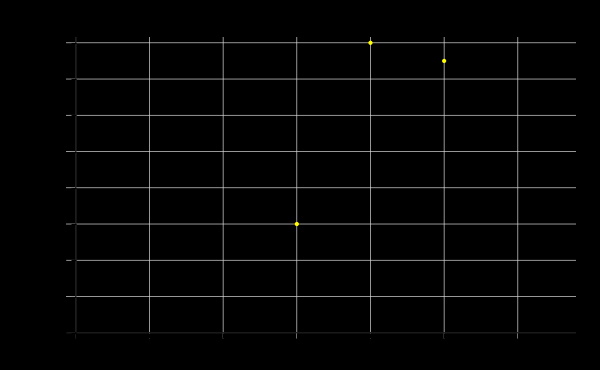
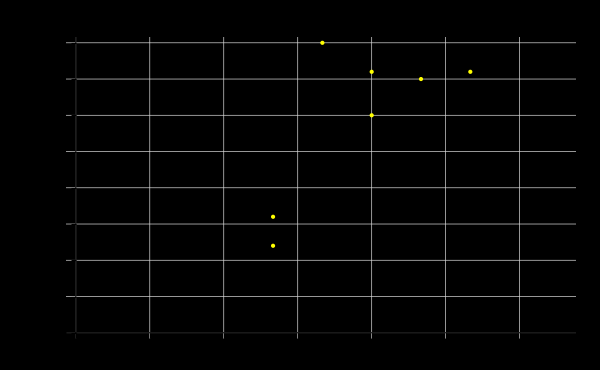
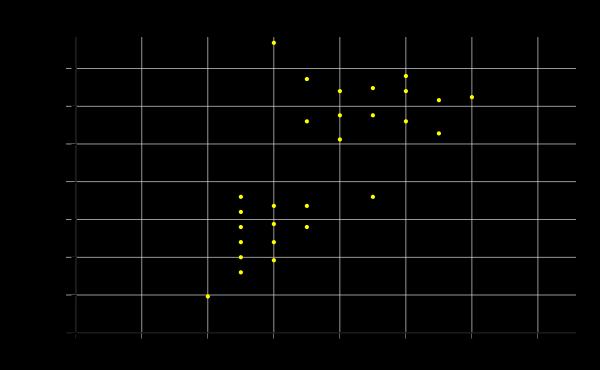
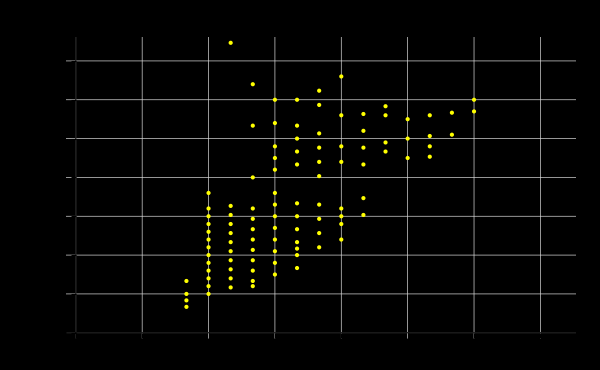
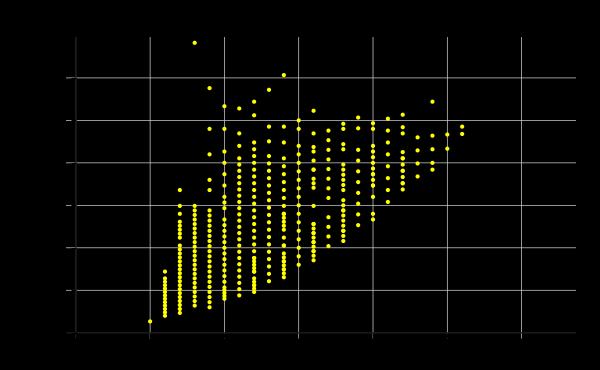
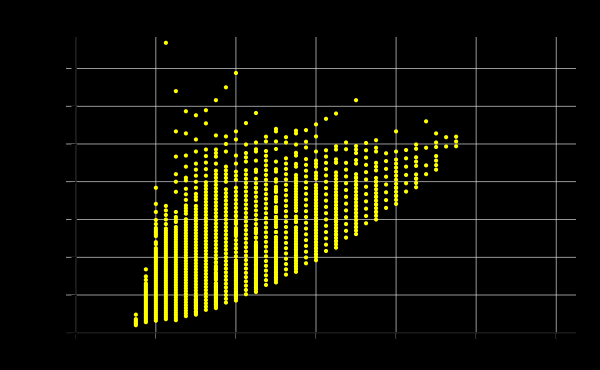
{-Graphics-min(a_1,a_2),-Graphics-min(a_1,a_2),-Graphics-min(a_1,a_2),-Graphics-min(a_1,a_2),-Graphics-min(a_1,a_2),-Graphics-min(a_1,a_2),-Graphics-min(a_1,a_2),-Graphics-min(a_1,a_2)}

```mathematica
MapIndexed[Labeled[ListPlot[(pt|->Tooltip[{Min@pt,Times@@pt},pt])/@#1,PlotRange->{{0,2^((#2[[1]])/2)Sqrt[#2[[1]]+1]+1},All},PlotStyle->{Yellow,PointSize[0.005]},Background->Black,AxesStyle->White,GridLines->Automatic,GridLinesStyle->Gray,AxesOrigin->{0,0},ImageSize->600,PlotLabel->Style["Min vs Product for families arising from even polytopes in dim "<>ToString[#2[[1]]],White,Background->Black],AxesLabel->{None,"a_1·a_2"}],Style["min(a_1,a_2)",White,Background->Black],Background->Black]&,Map[If[And@@EvenQ[#],{(#[[1]])/2+1,#[[2]]},Nothing]&,facetVertData,{2}]]
```

```mathematica
MapIndexed[Export["families-from-even-min-vs-prod-"<>ToString[#2[[1]]]<>".jpg",#1,Background->Black]&,%];
```

```mathematica
2^k(d-k+1)(2^(d-k)+k)-(2^k(d-k+1)+2^k(d-k)(2^(d-k-1)+k)+2^(d-1)d)//FullSimplify
```

-2^k (1+d-2 k)-2^(-1+d) (-2+k)

```mathematica
2^k(d-k+1)(2^(d-k)+k)-(2^k(d-k+1)+2^(k-1)(d-k+1)(2^(d-k)+k-1)+2^(κ-1)(d-κ)(2^(d-κ-1)+κ))//FullSimplify
```

-1/2 (2^d+2^k (-1+k)) (1+d-k)+2^k (-1-d+k)+(1+d-k) (2^d+2^k k)+1/4 (-d+κ) (2^d+2^(1+κ) κ)

Trying a subexact bound:

```mathematica
2^d(d-k+2)-(2^k(d-k+1)+2^(d-1)(d-k+1)+d 2^(d-1))//FullSimplify
```

-2^(-1+d) (-3+k)+2^k (-1-d+k)

```mathematica
Assuming[{k∈PositiveIntegers,d∈PositiveIntegers},Sum[t 2^(t-1),{t,1,d}]]
```

1-2^d+2^d d

```mathematica
Assuming[{k∈PositiveIntegers,d∈PositiveIntegers},Sum[t 2^(t-1),{t,1,d-k}]]
```

2^-k (-2^d+2^k+2^d d-2^d k)

```mathematica
Sum[t 2^(t-1),{t,d-k+1,d}]
```

2^(d-k) (1-2^k-d+2^k d+k)

```mathematica
FullSimplify[(d-k+1)2^(d-k)+Sum[t 2^(t-1),{t,d-k+1,d}]+(d-k+1)(2^(k+1)-2),Assumptions->{k∈PositiveIntegers,d∈PositiveIntegers}]
```

-2-2^d+2^(1+d-k)-2 d+2^d d+2^(1+k) (1+d-k)+2 k

```mathematica
2^k(d-k+1)(2^(d-k)+k)-((d-k+1)2^(d-k)+Sum[t 2^(t-1),{t,d-k+1,d}]+(d-k+1)(2^(k+1)-2))//FullSimplify
```

-2^-k (2+2^k (-2+k)) (2^d+2^k (-1-d+k))

```mathematica
((d-k+1)2^(d-k)+Sum[t 2^(t-1),{t,d-k+1,d}]+(d-k+1)(2^(k+1)-2))-2^k(d-k+1)(2^(d-k)+k)//FullSimplify
```

2^-k (2+2^k (-2+k)) (2^d+2^k (-1-d+k))

```mathematica
potenBound[d_,k_]:=2^d(d-1)+2^(d-k+1)+(2^(k+1)-2)(d-k+1)
```

```mathematica
(potenBound[d,k]-2^(d+1)-2^(d-U)potenBound[U,k+d-U]/.U->1)//FullSimplify
```

-2+2^(1-k) (-2+2^d)-2 d-(-2+2^d) k+2^(-1+k) (4 (1+d-k)+4^d (-3+d+k))

```mathematica
With[{expr=(potenBound[d,k]-2^(d+1)-2^(d-U)potenBound[U,k+d-U]/.U->5)},Grid[Table[With[{val=(expr/.{d->dd,k->kk})},Style[N[val,1],White,Background->If[val>=0,RGBColor[0.06, 0.42, 0.],RGBColor[1, 0, 0]]]],{dd,1,12},{kk,0,dd}],Frame->All,FrameStyle->Gray,Background->Black]]
```

-70. | -40. |  |  |  |  |  |  |  |  |  |  | 
-70. | -40. | -30. |  |  |  |  |  |  |  |  |  | 
-80. | -50. | -30. | -30. |  |  |  |  |  |  |  |  | 
-80. | -60. | -40. | -40. | -40. |  |  |  |  |  |  |  | 
-60. | -60. | -60. | -60. | -60. | -60. |  |  |  |  |  |  | 
-20. | -70. | -100. | -100. | -90. | 60. | 600. |  |  |  |  |  | 
100. | -60. | -200. | -200. | 100. | 1000. | 4000. | 10000. |  |  |  |  | 
400. | 20. | -90. | 400. | 2000. | 9000. | 30000. | 70000. | 200000. |  |  |  | 
1000. | 500. | 1000. | 5000. | 20000. | 50000. | 100000. | 300000. | 800000. | 2.×10^6 |  |  | 
3000. | 4000. | 10000. | 40000. | 100000. | 300000. | 700000. | 2.×10^6 | 4.×10^6 | 8.×10^6 | 2.×10^7 |  | 
10000. | 30000. | 70000. | 200000. | 500000. | 1.×10^6 | 3.×10^6 | 7.×10^6 | 2.×10^7 | 4.×10^7 | 8.×10^7 | 2.×10^8 | 
60000. | 200000. | 400000. | 1.×10^6 | 3.×10^6 | 6.×10^6 | 1.×10^7 | 3.×10^7 | 8.×10^7 | 2.×10^8 | 4.×10^8 | 8.×10^8 | 2.×10^9